### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

## Core parameters

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Simplex

```mathematica
imglist={};
For[γ=0,γ<=1.0,γ=γ+0.5,
dy1[y1_,y2_]:=y1(u ((q1^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_]:=y2 (u ((q2^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<=1&&Total[#]≥0&];
p1=ListPlot[relData,PlotStyle->{Black,PointSize[0.025]}];
(*p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];*)
p3=ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->{{Directive[cols⟦1⟧,PointSize[0.03]]},{Directive[cols⟦2⟧,PointSize[0.03]]},{Directive[cols⟦3⟧,PointSize[0.03]]}}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[p1,p3,p4];
cplt=ContourPlot[y1(u ((q1^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[y2 (u ((q2^2-(y1 q1^2+y2 q2^2+(1-y1-y2) q3^2))/(q1+q2+q3))+(1-u)(p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Blue]];
sp=StreamPlot[{dy1[y1,y2],dy2[y1,y2]},{y1,0,1},{y2,0,1},Frame->True,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0],RegionFillingStyle->None];
psim=Show[tlp,
Graphics[GeometricTransformation[First[Show[sp]],trans]],triangle,
Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],
Graphics[GeometricTransformation[First[Show[points]],trans]],
Graphics[GeometricTransformation[First[Show[ic]],trans]],
Graphics[Text["Copying intensity\n γ = "<>ToString[γ],{0.1,0.7}]],
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]
];(*,
Graphics[GeometricTransformation[First[parpl],trans]]*)
AppendTo[imglist,{γ,psim}]
]
```

```mathematica
BarLegend["CMYKColors"]
```

```mathematica
Show[imglist⟦6,2⟧,ImageSize->Large]
```

```mathematica
imglist⟦All,2⟧
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export[NotebookDirectory[]<>"gammadynamics.mov",imglist⟦All,2⟧]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/SimulationCode/mathematica/gammadynamics.mov

## Trajectory

```mathematica
initialconditions={
{0.4,0.3},
{0.4,0.4},
{0.3,0.3}
};
```

```mathematica
icplotsdata={};
Table[γ=0;
timeslist={};
For[γ=0,γ<=1.0,γ=γ+0.005,
solution=NDSolve[{
y1'[t]==y1[t] ((1-u)(p[γ,y1[t],q1] q1-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t])))),
y2'[t]==y2[t] ((1-u)(p[γ,y2[t],q2] q2-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t]))))
,y1[0]==initialconditions⟦z,1⟧,y2[0]==initialconditions⟦z,2⟧,WhenEvent[y1[t]>0.99||y2[t]>0.99||(1-y1[t]-y2[t])>0.99,AppendTo[timeslist,{γ,t,Position[{y1[t],y2[t],1-y1[t]-y2[t]},Max[y1[t],y2[t],1-y1[t]-y2[t]]]⟦1,1⟧}];"StopIntegration","LocationMethod"->"LinearInterpolation"]},{y1,y2},{t,200}];
];
splitdata=SplitBy[timeslist,Last];
AppendTo[icplotsdata,splitdata];
,{z,1,Length[initialconditions],1}]
```

{Null,Null,Null}

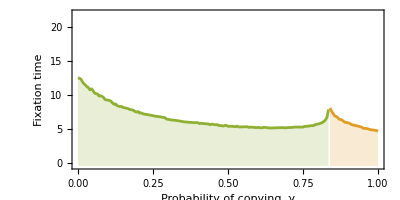

```mathematica
data=icplotsdata⟦1⟧;
ic1pl=ListPlot[Table[data⟦i⟧⟦All,1;;2⟧,{i,1,Length[data],1}],Joined->True,PlotRange->{All,{-0.5,22}},Filling->Bottom,PlotStyle->Table[cols⟦data⟦i⟧⟦1,3⟧⟧,{i,1,Length[data],1}],AspectRatio->1/2,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Fixation time",FontFamily->"Calibri",18]},Background->White]
```

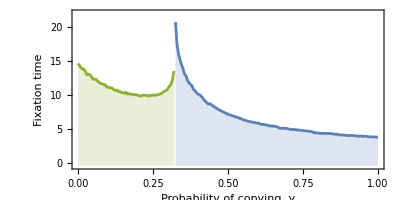

```mathematica
data=icplotsdata⟦2⟧;
ic2pl=ListPlot[Table[data⟦i⟧⟦All,1;;2⟧,{i,1,Length[data],1}],Joined->True,PlotRange->{All,{-0.5,22}},Filling->Bottom,PlotStyle->Table[cols⟦data⟦i⟧⟦1,3⟧⟧,{i,1,Length[data],1}],AspectRatio->1/2,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Fixation time",FontFamily->"Calibri",18]},Background->White]
```

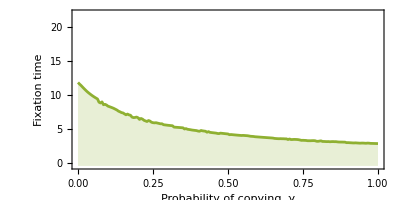

```mathematica
data=icplotsdata⟦3⟧;
ic3pl=ListPlot[Table[data⟦i⟧⟦All,1;;2⟧,{i,1,Length[data],1}],Joined->True,PlotRange->{All,{-0.5,22}},Filling->Bottom,PlotStyle->Table[cols⟦data⟦i⟧⟦1,3⟧⟧,{i,1,Length[data],1}],AspectRatio->1/2,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{Style["Probability of copying, γ",FontFamily->"Calibri",18],Style["Fixation time",FontFamily->"Calibri",18]},Background->White]
```

```mathematica
γ=1;
solution=NDSolve[{
y1'[t]==y1[t] ((p[γ,y1[t],q1] q1-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t])))),
y2'[t]==y2[t] ((p[γ,y2[t],q2] q2-(p[γ,y1[t],q1] q1 y1[t]+p[γ,y2[t],q2] q2 y2[t]+p[γ,(1-y1[t]-y2[t]),q3] q3 (1-y1[t]-y2[t]))))
,y1[0]==0.4,y2[0]==0.3},{y1,y2},{t,100}]
```

{{y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

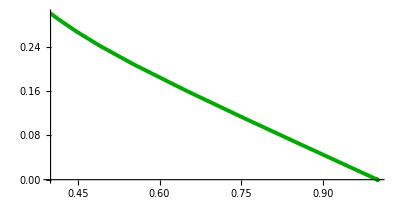

```mathematica
pp=ParametricPlot[Evaluate[{y1[t],y2[t]}/.solution],{t,0,20},PlotRange->All,PlotStyle->Directive[Darker[Green],Thickness[0.007]]]
```

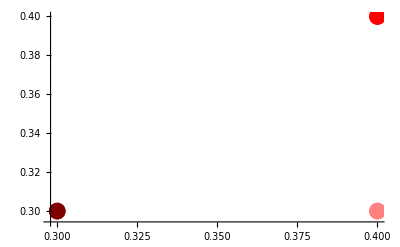

```mathematica
ic=ListPlot[{{initialconditions⟦1⟧},{initialconditions⟦2⟧},{initialconditions⟦3⟧}},PlotStyle->{{Directive[Lighter[Red,0.5],PointSize[0.03]]},{Directive[Red,PointSize[0.03]]},{Directive[Darker[Red,0.5],PointSize[0.03]]}}]
```

```mathematica
tlp=TernaryListPlot[{0.3,0.3,0.3},(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧]
```

```mathematica
Show[tlp,
Graphics[GeometricTransformation[First[Show[sp]],trans]],triangle,
Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],
Graphics[GeometricTransformation[First[Show[points]],trans]],
Graphics[GeometricTransformation[First[Show[ic]],trans]],
Graphics[GeometricTransformation[First[Show[pp]],trans]],
Graphics[Text["Copying intensity\n γ = "<>ToString[γ],{0.1,0.7}]],
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]
]
```

-Graphics-